```mathematica
Needs["Benchmarking`"]
```

```mathematica
BenchmarkReport[]
```

4hga6_shm50FrontEndObject[LinkObject["4hga6_shm", 3, 1]]50WolframMark Report

## CPUUUUUuUUUUUUuuuwuwuuuuwuuuww

If paralleldo is much faster than do or almost the same, take paralleldo : do = 7 : 3
Cuz for my understanding, one benifits much more for multi core, and one benifits much more for high frequency per core, no? 

if parado slower than do, take only do

```mathematica
CloseKernels
```

CloseKernels

```mathematica
SetAttributes[Timer,{HoldAll}];
SinglePrimee[a_] := Do[If[PrimeQ[q] == True, 1, 0], {q, 0, a}];
ParaPrime[a_] := ParallelDo[If[PrimeQ[q] == True, 1, 0], {q, 0, a}];
Timer[expr_] :=
  Block[
  {result},
  ClearSystemCache[];
  result = AbsoluteTiming[expr];
  Return[result[[1]]]
 ];
```

```mathematica
TestSet[] := Module[
{
FindPI, SinFindPrime, ParaFindPrime, Amountofpi = 10^7.5, newtonIteration, CompileTIme,
EigenTimePara, EigenTimeSing, LinearSysSing, LinearSysPara, TransposeTime, 
RandomsortPara, RandomsortSing, Render3Dtime, NSloveTimePara, NSloveTimeSingle
},

  FindPI = Timer[N[π, 10000000];];
  SinFindPrime = Timer[SinglePrimee[Amountofpi];];
  ParaFindPrime = Timer[ParaPrime[Amountofpi];];
     newtonIteration = Compile[{{z, _Complex}, {n, _Integer}}, Module[{zn = z}, Do[zn = (2 zn + 1/zn^2)/3, {n}];
        If[Re[zn] > 0, 1, If[Im[zn] > 0, 2, 3]]], RuntimeAttributes -> {Listable}, Parallelization -> True];
  CompileTIme = Timer[ArrayPlot[Table[newtonIteration[x + I*y, 25], {y, -5, 5, 2./199}, {x, -5, 5, 2./199}]]];
  
  EigenTimePara = Module[{a, b, m}, Timer[SeedRandom[1]; a = RandomReal[{}, {1500, 1500}]; b = DiagonalMatrix[RandomReal[{}, {1500}]]; m = a.b.Inverse[a]; 
                  ParallelDo[Eigenvalues[m], {10}]]];
  EigenTimeSing = Module[{a, b, m}, Timer[SeedRandom[1]; a = RandomReal[{}, {1500, 1500}]; b = DiagonalMatrix[RandomReal[{}, {1500}]]; m = a.b.Inverse[a]; 
                  Do[Eigenvalues[m], {10}]]];
  LinearSysSing = Module[{m, v}, Timer[SeedRandom[1]; m = RandomReal[{}, {5000, 5000}]; v = RandomReal[{}, {5000}]; Do[LinearSolve[m, v], {10}]]];
  LinearSysPara = Module[{m, v}, Timer[SeedRandom[1]; m = RandomReal[{}, {5000, 5000}]; v = RandomReal[{}, {5000}]; ParallelDo[LinearSolve[m, v], {10}]]];
  TransposeTime = Module[{m}, Timer[SeedRandom[1]; m = RandomReal[{}, {8000, 8000}]; Do[Transpose[m], {10}]]];
  RandomsortPara = Module[{a}, Timer[SeedRandom[1]; a = RandomInteger[{1, 10^10}, {3*10^6}]; ParallelDo[Sort[a], {10}]]];
  RandomsortSing = Module[{a}, Timer[SeedRandom[1]; a = RandomInteger[{1, 10^10}, {3*10^6}]; Do[Sort[a], {10}]]];
  Render3Dtime = RepeatedTiming[SphericalPlot3D[1 + Sin[5 ϕ] Sin[10 θ]/10, {θ, 0, 2 π}, {ϕ, 0, 4 π}, ColorFunction -> (ColorData["Rainbow"][#6] &), 
                 Mesh -> None, PlotPoints -> 200, Boxed -> False, Axes -> False];][[1]];
  NSloveTimePara = RepeatedTiming[Parallelize[NSolve[Sin[z + Sin[z + Sin[z]]] == Cos[z + Cos[z + Cos[z]]] && -2 < Re[z] < 2 && -2 < Im[z] < 2, z];]][[1]];
  NSloveTimeSingle = RepeatedTiming[NSolve[Sin[z + Sin[z + Sin[z]]] == Cos[z + Cos[z + Cos[z]]] && -2 < Re[z] < 2 && -2 < Im[z] < 2, z];][[1]];
  
  
  
  <|"PITime" -> FindPI, "FindPrimeSingle" -> SinFindPrime, 
  "FindPrimePara" -> ParaFindPrime, 
  "CompileTime" -> CompileTIme, 
  "EigenTimePara" -> EigenTimePara, 
  "EigenTimeSingle" -> EigenTimeSing, "LinearSystemSingle" -> LinearSysSing, 
  "LinearSystemPara" -> LinearSysPara, "TransposeTime" -> TransposeTime, 
  "SortRandomPara" -> RandomsortPara, "SortRandomSingle" -> RandomsortSing, 
  "Render3DTime" -> Render3Dtime, "NSloveTimePara" -> NSloveTimePara, 
  "NSloveTimeSingle" -> NSloveTimeSingle|>
  ]
```

```mathematica
Score[t_]:=-900*ArcTan[0.02*t]+900;
```

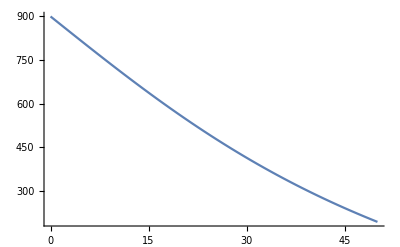

```mathematica
Plot[-900*ArcTan[0.02x]+900,{x,0,50},PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
CPUScore:= (
CPUTestResult=TestSet[];
Score[CPUTestResult["PITime"]]+

(3*Score[CPUTestResult["FindPrimeSingle"]]+7*Score[CPUTestResult["FindPrimePara"]])/10+
Score[CPUTestResult["CompileTime"]]+

(3*Score[CPUTestResult["EigenTimeSingle"]]+7*Score[CPUTestResult["EigenTimePara"]])/10+
(Score[CPUTestResult["LinearSystemSingle"]]+Score[CPUTestResult["LinearSystemPara"]])/2+
Score[CPUTestResult["TransposeTime"]]+

(7*Score[CPUTestResult["SortRandomPara"]]+3*Score[CPUTestResult["SortRandomSingle"]])/10+

1.5*Score[CPUTestResult["Render3DTime"]]+

(7*Score[CPUTestResult["NSloveTimePara"]]+3*Score[CPUTestResult["NSloveTimeSingle"]])/10)
```

```mathematica
CPUScore
```

7345.97

```mathematica
CPU:=(CloseKernels[];LaunchKernels[6];
SetAttributes[Timer,{HoldAll}];
Timer[expr_] :=
Block[
{result},
ClearSystemCache[];
result = AbsoluteTiming[expr];
  Return[result[[1]]]
];
TestSet;
CPUScore
)
```

```mathematica
CPU
```

6517.2

```mathematica
CloseKernels[];
LaunchKernels[6]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local]}

```mathematica
SetAttributes[Timer,{HoldAll}];
Timer[expr_] :=
Block[
{result},
ClearSystemCache[];
result = AbsoluteTiming[expr];
  Return[result[[1]]]
]
```

```mathematica
FindPI=Timer[N[π,10000000];]
```

4.32124

```mathematica
SinglePrimee[a_]:=Do[If[PrimeQ[q]==True,1,0],{q,0,a}];
```

```mathematica
ParaPrime[a_]:=ParallelDo[If[PrimeQ[q]==True,1,0],{q,0,a}];
```

```mathematica
SinFindPrime=Timer[SinglePrimee[10^7.5];]
```

21.9599

```mathematica
ParaFindPrime=Timer[ParaPrime[10^7.5];]
```

3.84645

```mathematica
(*what's the percentage of parallel function in Mathhematica? *)
```

```mathematica
newtonIteration=Compile[{{z,_Complex},{n,_Integer}},Module[{zn=z},Do[zn=(2zn+1/zn^2)/3,{n}];
If[Re[zn]>0,1,If[Im[zn]>0,2,3]]],RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
CompileTIme=Timer[ArrayPlot[Table[newtonIteration[x+I*y,25],{y,-5,5,2./199},{x,-5,5,2./199}]]]
```

4.90032

```mathematica
EigenTimePara=Module[{a,b,m},Timer[SeedRandom[1];a=RandomReal[{},{1500,1500}];b=DiagonalMatrix[RandomReal[{},{1500}]];m=a.b.Inverse[a];ParallelDo[Eigenvalues[m],{10}]]]
```

7.55197

```mathematica
EigenTimeSing=Module[{a,b,m},Timer[SeedRandom[1];a=RandomReal[{},{1500,1500}];b=DiagonalMatrix[RandomReal[{},{1500}]];m=a.b.Inverse[a];Do[Eigenvalues[m],{10}]]]
```

9.62016

```mathematica
LinearSysSing=Module[{m,v},Timer[SeedRandom[1];m=RandomReal[{},{5000,5000}];v=RandomReal[{},{5000}];Do[LinearSolve[m,v],{10}]]]
```

7.63992

```mathematica
LinearSysPara=Module[{m,v},Timer[SeedRandom[1];m=RandomReal[{},{5000,5000}];v=RandomReal[{},{5000}];ParallelDo[LinearSolve[m,v],{10}]]]
```

8.79459

```mathematica
TransposeTime=Module[{m},Timer[SeedRandom[1];m=RandomReal[{},{8000,8000}];Do[Transpose[m],{10}]]]
```

3.72768

```mathematica
RandomsortPara=Module[{a},Timer[SeedRandom[1];a=RandomInteger[{1,10^10},{3*10^6}];ParallelDo[Sort[a],{10}]]]
```

1.82161

```mathematica
RandomsortSing=Module[{a},Timer[SeedRandom[1];a=RandomInteger[{1,10^10},{3*10^6}];Do[Sort[a],{10}]]]
```

4.73785

```mathematica
(*Need one for NDSlove (or find root if doesn't work out), but I couln't think of any long differential equation that takes time to solve*)

(*Is the 3D plot render by CPU or GPU?*)

(*I got 7 tests for GPU so far, just meed one for NDSlove and maybe one for rendering, don't need too many tests cuz the result is kinda consistant for performance*)

(*want to do a loading bar for benchmark*)

(*I am not showing the actual time to load each test, instead, just a score in the end *)


(*all tests should be around 3 ~ 10 ish second on my machine , so usually the whole test run for CPU will take around 1 ~ 3 min depends on the different laptop, a bit longer than the current benchmark, but it's normal and I think will be more accurate*)
```

```mathematica
Render3Dtime=RepeatedTiming[SphericalPlot3D[1+Sin[5 ϕ] Sin[10 θ]/10,{θ,0,2π},{ϕ,0,4π},ColorFunction->(ColorData["Rainbow"][#6]&),Mesh->None,PlotPoints->200,Boxed->False,Axes->False];][[1]]
```

7.62

```mathematica
NSloveTimePara=RepeatedTiming[Parallelize[NSolve[Sin[z+Sin[z+Sin[z]]]==Cos[z+Cos[z+Cos[z]]]&&-2<Re[z]<2&&-2<Im[z]<2,z];]]
```

{4.55,Null}

```mathematica
NSloveTimeSingle=RepeatedTiming[NSolve[Sin[z+Sin[z+Sin[z]]]==Cos[z+Cos[z+Cos[z]]]&&-2<Re[z]<2&&-2<Im[z]<2,z];]
```

{4.6,Null}

## RAMMMMMMAMMAMMMAMAMM

```mathematica
RAMSpeedTest[] := Module[{
AA,A,B,CC,AASize={2000,2000},ASize={5000,5000},
BSize={10000,10000},CCSize={15000,15000},Speed,Time,Score
},
Speed=UnitConvert[Quantity[
D[Fit[{
{RepeatedTiming[AA=ConstantArray[0.,AASize]][[1]],ByteCount[AA]},
{RepeatedTiming[A=ConstantArray[0.,ASize]][[1]],ByteCount[A]},
{RepeatedTiming[B=ConstantArray[0.,BSize]][[1]],ByteCount[B]},
{RepeatedTiming[CC=ConstantArray[0.,CCSize]][[1]],ByteCount[CC]}},
{1,x},x],x],
"Bytes"/"Seconds"],"Megabytes"/"Seconds"];

ClearAll[A,B,CC,AA];
Score=QuantityMagnitude[Speed]/10;
<|"RAMSpeed" -> Speed,"RAMScore" -> Score|>
]
```

```mathematica
RAMSpeedTest[]
```

<|RAMSpeed→2000. MB/s,RAMScore→200.|>

```mathematica
RAMMuch[]:=
Module[{Weight=350,HowMuch,Score},
Score=Weight*Sqrt[
QuantityMagnitude[HowMuch=SystemInformation["Machine","PhysicalTotal"]]]
;
<|"RAMScore" -> Score,"RAMTotal" -> HowMuch|>
]
```

```mathematica
RAMMuch[]
```

<|RAMScore→1196.27,RAMTotal→15.9008 GiB|>

1196.27

```mathematica
RAMMuch[]["RAMScore"]
```

1196.27

```mathematica
RAMScore:=(RAMMuch[]["RAMScore"]+RAMSpeedTest[]["RAMScore"])
```

```mathematica
RAMScore
```

1604.91

## DiskKKKKKKKKKKKK

```mathematica
ClearAll[DiskSpeed]
```

```mathematica
DiskSpeed[] := Module[
	{
	strLength = 500000000, str, testfile,
	diskwritetime, diskreadtime, diskwritespeed,
	diskreadspeed
	}
	,
	str = StringJoin[ConstantArray["0", strLength]];
	testfile = CreateFile[];
	diskwritetime = First@AbsoluteTiming[WriteString[testfile, str]];
	diskreadtime = First@RepeatedTiming[ReadString[testfile]];
	
	diskwritespeed = UnitConvert[
		Quantity[ByteCount[str]/diskwritetime, "Bytes"/"Seconds"],
		"Megabytes"/"Seconds"
		];
	diskreadspeed = UnitConvert[
		Quantity[ByteCount[str]/diskreadtime, "Bytes"/"Seconds"],
		"Megabytes"/"Seconds"
		];
	
	<|"ApparentDiskWriteSpeed" -> diskwritespeed, "ApparentDiskReadSpeed" -> diskreadspeed|>
]
```

```mathematica
DiskScore:=QuantityMagnitude[(DiskSpeed[]["ApparentDiskWriteSpeed"]+DiskSpeed[]["ApparentDiskReadSpeed"])]
```

```mathematica
DiskScore
```

620.288

```mathematica
res=DiskSpeed[]
```

<|ApparentDiskWriteSpeed→30.8621 MB/s,ApparentDiskReadSpeed→561. MB/s|>

```mathematica
Merge[{<|"WriteSpeed"->Quantity[32.31107349700604, ("Megabytes")/("Seconds")],"ReadSpeed"->Quantity[595.6337810552985352309`3., ("Megabytes")/("Seconds")]|>,<|"RamWriteSpeed"-> …|>}, First]
```

<|WriteSpeed→32.3111 MB/s,ReadSpeed→596. MB/s,RamWriteSpeed→…|>

```mathematica
res["ReadSpeed"]
```

596. MB/s

```mathematica
QuantityMagnitude[res["WriteSpeed"]]
```

32.3111

## GPUUU~~

```mathematica
Needs["CUDALink`"];
CUDAResourcesInstall["<path_to_paclet>", Update->True];
GPUTest[]:=Module[
{
A,B,randomsize={8000,8000},dottime,transposetime,foot,
nettest,convNet,dottrainingData,convtrainingData,dottrained,
dottraintime,convtime,convtrained,randomobject,
trainingDataforimage,classesforimage,moduleforimage,
netforimage,timeforimage,trainedimage

},
A=RandomReal[{-50,50},randomsize];
B=RandomReal[{-50,50},randomsize];
dottime=RepeatedTiming[CUDADot[A,B];][[1]];
foot=Entity["AnimalAnatomicalStructure","LeftForefoot::CanisLupusFamiliaris::4t62p"];
transposetime=RepeatedTiming[CUDATranspose/@ColorSeparate[
	AnatomyPlot3D[{foot}]];][[1]];
nettest=NetChain[{100,BatchNormalizationLayer[],Ramp,
	300,BatchNormalizationLayer[],Ramp,300,Ramp,45,Ramp,90},
	"Input"->{80,80}];
convNet=NetChain[{ConvolutionLayer[16,3],
	BatchNormalizationLayer[],Ramp,ConvolutionLayer[32,3],
	BatchNormalizationLayer[],Ramp,ConvolutionLayer[64,3],
	BatchNormalizationLayer[],Ramp,ConvolutionLayer[17,3],
	AggregationLayer[Max]},"Input"->{80,80}];
dottrainingData=<|"Input"->RandomReal[1,{1000,80,80}],
	"Output"->RandomReal[{-20,20},{1000,90}]|>;
{dottraintime,dottrained}=RepeatedTiming@NetTrain[nettest,dottrainingData,
	TargetDevice->"GPU",MaxTrainingRounds->120,
	TrainingProgressReporting->None];
convtrainingData=<|"Input"->RandomReal[1,{1000,80,80}],
	"Output"->RandomReal[{-20,20},{1000,17}]|>;
{convtime,convtrained}=RepeatedTiming@NetTrain[convNet,convtrainingData,
	TargetDevice->"GPU",MaxTrainingRounds->120,
	TrainingProgressReporting->None];
randomobject=ResourceObject["CIFAR-10"];
	trainingDataforimage=ResourceData[randomobject,"TrainingData"];
	RandomSample[trainingData,3];	
	classesforimage=Union@Values[trainingDataforimage];
	moduleforimage=NetChain[{ConvolutionLayer[20,{3,3}],BatchNormalizationLayer[],
	ElementwiseLayer[Ramp],PoolingLayer[{3,3},"PaddingSize"->1]}];	
	netforimage=NetChain[{moduleforimage,moduleforimage,FlattenLayer[],200,Ramp,10,
	SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{32,32}}],
	"Output"->NetDecoder[{"Class",classesforimage}]];
{timeforimage,trainedimage}=RepeatedTiming@NetTrain[netforimage,trainingDataforimage,
	TargetDevice->"GPU",MaxTrainingRounds->2,
	TrainingProgressReporting->None];	
	
<|"CUDADotTime" -> dottime,"CUDATransposeTime" -> transposetime,
"TrainDotTime"-> dottraintime, "TrainConvLayerTime"-> convtime,
"TrainImageTime"-> timeforimage
|>

]
```

```mathematica
Score[t_]:=-900*ArcTan[0.02*t]+900;
```

```mathematica
GPUScore:=(GPUTestResult=GPUTest[];
Score[GPUTestResult["CUDADotTime"]]+
Score[GPUTestResult["CUDATransposeTime"]]+
Score[GPUTestResult["TrainDotTime"]]+
Score[GPUTestResult["TrainConvLayerTime"]]+
Score[GPUTestResult["TrainImageTime"]]
)
```

```mathematica
GPUScore
```

3989.83

```mathematica
A=RandomReal[{-50,50},{9000,9000}];
B=RandomReal[{-50,50},{9000,9000}];
```

```mathematica
RepeatedTiming[CUDADot[A,B];]
```

{8.91,Null}

```mathematica
RepeatedTiming[CUDATranspose/@ColorSeparate[AnatomyPlot3D[{Entity["AnimalAnatomicalStructure","LeftForefoot::CanisLupusFamiliaris::4t62p"]}]];]
```

{1.203,Null}

```mathematica
Instuff=RandomReal[1,20000];
Net=NetInitialize[LinearLayer[20000, "Input"-> 20000]];
AbsoluteTiming[Net[Instuff, TargetDevice->"GPU"];]
```

{0.518856,Null}

```mathematica
obj=ResourceObject["CIFAR-10"];
trainingData=ResourceData[obj,"TrainingData"];
RandomSample[trainingData,3]
```

{-Graphics-→frog,-Graphics-→automobile,-Graphics-→bird}

```mathematica
classes=Union@Values[trainingData]
```

{airplane,automobile,bird,cat,deer,dog,frog,horse,ship,truck}

```mathematica
module=NetChain[{ConvolutionLayer[20,{3,3}],BatchNormalizationLayer[],ElementwiseLayer[Ramp],PoolingLayer[{3,3},"PaddingSize"->1]}];

net=NetChain[{module,module,FlattenLayer[],200,Ramp,10,SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{32,32}}],"Output"->NetDecoder[{"Class",classes}]];
```

```mathematica
{time,trained}=AbsoluteTiming@NetTrain[net,trainingData,TargetDevice->"GPU",MaxTrainingRounds->2,TrainingProgressReporting->"Panel"];
```

```mathematica
time
```

8.60434

```mathematica
net=NetChain[{100,BatchNormalizationLayer[],Ramp,300,BatchNormalizationLayer[],Ramp,400,Ramp,90},"Input"->{80,80}]
```

NetChain[<>]

```mathematica
convNet=NetChain[{ConvolutionLayer[16,3],BatchNormalizationLayer[],Ramp,ConvolutionLayer[32,3],BatchNormalizationLayer[],Ramp,ConvolutionLayer[64,3],BatchNormalizationLayer[],Ramp,ConvolutionLayer[10,3],AggregationLayer[Max]},"Input"->{50,50}]
```

NetChain[<>]

```mathematica
trainingData=<|"Input"->RandomReal[1,{1000,80,80}],"Output"->RandomReal[{-20,20},{1000,90}]|>;
```

```mathematica
{time,trained}=AbsoluteTiming@NetTrain[net,trainingData,TargetDevice->"GPU",MaxTrainingRounds->120,TrainingProgressReporting->"Panel"];
```

```mathematica
time
```

5.12103

```mathematica
DialogInput
```

```mathematica
{time,trained}=AbsoluteTiming@NetTrain[net,trainingData,TargetDevice->"CPU",MaxTrainingRounds->100,TrainingProgressReporting->None];
```

```mathematica
time
```

2.28533

#### ConvNet

```mathematica
{time,trained}=AbsoluteTiming@NetTrain[convNet,trainingData,TargetDevice->"GPU",MaxTrainingRounds->100,TrainingProgressReporting->None];
```

```mathematica
time
```

3.06011

```mathematica
{time,trained}=AbsoluteTiming@NetTrain[convNet,trainingData,TargetDevice->"CPU",MaxTrainingRounds->100,TrainingProgressReporting->None];
```

NetTrain::invindim3: Data provided to port "Input" should be a non-empty list of 50×50 matrices of real numbers, but was a 800×80×80 array of real numbers.

```mathematica
time
```

2.92144

```mathematica
trained
```

NetChain[<>]

```mathematica
in=RandomReal[1,200];
net=NetInitialize[LinearLayer[500, "Input"-> 200]]
LinearLayer[<>]
Get["MXNetLink`"]
MXNetLink`$HasGPU
$MXGPUEnabledQ
False
?*`*GPU*

{{}, {}, {}, {}, {}}
net[in];//AbsoluteTiming
{0.0069521,Null}
net[in, TargetDevice->"GPU"];//RepeatedTiming
{0.0004262138135593218`2.,Null}
```

```mathematica
NeuralNetworks`Private`GetGPUInformation[]
```

{<|TotalMemory→3517421977,FreeMemory→8589934592|>}

```mathematica
Needs["CUDALink`"]
```

```mathematica
src="
__global__ void mandelbrot_kernel(unsigned char * set, float zoom, float bailout, mint width, mint height) 
{
   int xIndex = threadIdx.x + blockIdx.x*blockDim.x;
   int yIndex = threadIdx.y + blockIdx.y*blockDim.y;
   int k;

   Real_t x0 = zoom*(width/3 - xIndex);
   Real_t y0 = zoom*(height/2 - yIndex);
   Real_t tmp, x = 0, y = 0;

   if (xIndex < width && yIndex < height) {
       for (k = 0; (x*x+y*y <= bailout) && (k < 511); k++) {
            tmp = x*x - y*y +x0;
            y = 2*x*y + y0;
            x = tmp;
        };
        set[xIndex + yIndex*width] = (unsigned char)(k/2);
    }
}
";
```

```mathematica
mfun:=CUDAFunctionLoad[acc,"mandelbrot_kernel",{{"Byte",_,"Output"},"Float","Float",_Integer,_Integer},{16,16}]
```

```mathematica
{width,height}={480,480}
```

{480,480}

```mathematica
mset=CUDAMemoryAllocate["UnsignedByte",{height,width}];
```

```mathematica
res=mfun[mset,0.005,8.0,width,height,{width,height}];//RepeatedTiming
```

CUDAFunctionLoad::invprog: CUDALink encountered an invalid program.

General::stop: Further output of CUDAFunctionLoad::invprog will be suppressed during this calculation.

{0.000038,Null}

```mathematica
Image[CUDAMemoryGet[First[res]],"Bit"]
```

```mathematica
acc="__global__ void Prime(mint end)

int n = threadIdx.x + blockIdx.x*blockDim.x;
Int64 start=11;
Int64 end;
for (n=start;n<start+end;n+=2)
{end=Math.Sqrt(n);
for (Int64 i=2;i≤end;i+=2) {if ((n % i)==0) break;
if (i==end) isPrime(n);}
";
```

```mathematica
add:=CUDAFunctionLoad[acc,"Prime",{321},256]
```

```mathematica
add
```

CUDAFunctionLoad::cmperr: -- Message text not found -- (C:\Users\dali7\AppData\Roaming\Mathematica\Paclets\Repository\CUDA….0.359\CUDAToolkit\bin/../include\cuda.h(55): error: expected a "{")

CUDAFunctionLoad::cmperr: -- Message text not found -- (C:\Users\dali7\AppData\Roaming\Mathematica\Paclets\Repository\CUDA…../include\cuda.h(435): error: identifier "cuuint32_t" is undefined)

CUDAFunctionLoad::cmperr: -- Message text not found -- (C:\Users\dali7\AppData\Roaming\Mathematica\Paclets\Repository\CUDA…../include\cuda.h(436): error: identifier "cuuint64_t" is undefined)

General::stop: Further output of CUDAFunctionLoad::cmperr will be suppressed during this calculation.

CUDAFunctionLoad[__global__ void Prime(mint end)
#include<stdio.h>
#include<cuda.h>
#include<math.h>

Int64 start=11;
Int64 end;
for (Int64 n=start;n<start+end;n+=2)
{end=Math.Sqrt(n);
for (Int64 i=2;i≤end;i+=2) {if ((n % i)==0) break;
if (i==end) isPrime(n);}
,Prime,{321},256]

```mathematica
CUDAQ[]
```

True